# Chapter. Potential steps and potential pulses

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter8”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter8”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->137,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12], Cell[TextData[{"Potential steps and potential pulses"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Chronoamperometry","Staircase voltammetry","Normal pulse voltammetry","Differential pulse voltammetry","Summary","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[];
Symbolize[Subscript[𝒟, _]];
Symbolize[Subscript[k, _]];
```

```mathematica
SetOptions[ListPlot,
Axes-> False,
BaseStyle->Directive[FontFamily->"Arial",10,Plain],
FrameLabel-> None,
Frame->True,
FrameTicks-> Automatic,
GridLines-> None,
ImageSize->288,
Joined-> True,
PlotLabel-> None];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily->"Arial",10,Plain],
FrameLabel-> None,
Frame->True,
FrameTicks-> Automatic,
GridLines-> None,
ImageSize->288,
PlotStyle-> GrayLevel[0],
PlotLabel-> None];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
optionA={
PlotStyle-> Black,
FrameTicks:>{ticks1[0,20000,5000,5],ticks1[2.,-2.,-.5,5],ticks2[0,20000,5000,5],ticks2[2.,-2.,-.5,5]},
FrameLabel->{"increments","χ",None,None},
ImagePadding->{{Inherited,10},{Inherited,5}}};
```

```mathematica
optionA1={
PlotStyle-> Black,
FrameTicks:>{ticks1[0,20000,5000,5],ticks1[0.2,-2.,-.2,5],ticks2[0,20000,5000,5],ticks2[0.2,-2.,-.2,5]},
FrameLabel->{"increments","χ",None,None},
ImagePadding->{{Inherited,5},{Inherited,5}}
};
```

```mathematica
optionA2={
PlotStyle-> Black,
FrameTicks:>{ticks1[0,500,100,5],ticks1[2.,-6.,-2.,5],ticks2[0,500,100,5],ticks2[2.,-6.,-2.,5]},
FrameLabel->{"increments","χ",None,None},
ImagePadding->{{Inherited,5},{Inherited,5}}
};
```

```mathematica
(*options for voltammograms*)
optionB={
PlotStyle-> Black,
FrameTicks:>{ticks1[-10,10,5,5],ticks1[.2,-1.2,-.2,5],ticks2[-10,10,5,5],ticks2[.2,-1.2,-.2,5]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],
Style["χ",FontFamily-> "Times New Roman",Italic,10],None,None},
ImagePadding->{{Inherited,5},{Inherited,5}}
};
```

```mathematica
optionDC={
PlotRange-> {{-10,10},{-0.5,0.02}},
FrameTicks:>{ticks1[-10,10,5,5],ticks1[0.2,-1.,-.2,5],ticks2[-10,10,5,5],ticks2[0.2,-1.,-.2,5]},
FrameLabel-> {Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],χ,None,None}
};
```

```mathematica
optionDC2={
PlotRange-> {{-30,0},{-0.4,0.02}},
FrameTicks:>{ticks1[-30,10,5,5],ticks1[0.2,-1.,-.2,5],ticks2[-30,10,5,5],ticks2[0.2,-1.,-.2,5]},
FrameLabel-> {Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],χ,None,None},
ImagePadding->{{Inherited,5},{Inherited,5}}
};
```

```mathematica
(* options for power spectrum plots *)
optionMain={
PlotStyle->{Black,AbsoluteThickness[0.5]},
FrameTicks:>{ticks1[0,40,5,5],ticks1[0.,.2,.05,5],ticks2[0,40,5,5],ticks2[0.,.2,.05,5]},
FrameLabel->{"Dimensionless frequency",None,None,None},
ImagePadding->{{Inherited,5},{Inherited,5}}
};
```

```mathematica
optionD={
PlotStyle-> Black,
FrameLabel->{"increments","χ",None,None}
};
```

```mathematica
optionDiff={
PlotRange-> {{-8,8},{-1.5,0.75}},
FrameLabel-> {Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic],χ,None,None}
};
```

```mathematica
ClearAll[𝒻,F,R,T,𝒟,α];

F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T = 298.; (*Absolute temperature*)
𝒻=F/(R*T);
𝒟=1.*10^-5;(*diffusion coefficient of substrate in cm^2 s^-1*)
α=0.5; (*transfer coefficient*)
```

```mathematica
Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;

Protect[InverseLaplaceTransform];
```

Required for Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][cR][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][CR[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];

LaplaceTransform[Derivative[d__][cO][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][CO[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];]
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

Potential steps to the limiting current region were examined in Chapter 1. This chapter extends the analysis to include potential steps to any potential, double potential steps and quasi reversible reactions. On one hand staircase voltammetry, which is the digital implementation of cyclic voltammetry usually employed in commercial instrumentation, can be thought of as a series of potential steps and thus simulation methods for staircase voltammetry follow the section on chronoamperometry. On the other hand staircase voltammetry can also be considered to be the combination of a sawtooth waveform superimposed on a linear potential sweep and therefore the Fourier transform methods described in the previous chapter can be applied to the staircase simulation. In the final sections of this chapter normal pulse and differential pulse voltammograms are simulated by substituting the waveform for staircase voltammetry with the respective waveforms (pulse-forms) for normal and differential pulse voltammetry.

## Chapter.Section Chronoamperometry

Chapter.Section.Subsection Potential Step

The equation for a potential step to the limiting current region was derived in Chapter 1. In this section we concern ourselves with potential steps to non-limiting current potential regions and double potential steps. Taking the Laplace transform of Fick’s second law for semi-infinite diffusion and assuming that the reduced form is not initially present we arrive at

(c^-)_O(x, s)=c_O^*/s+Bexp(-(x(s/D_O))^(1/2))

and

(c^-)_R(x, s)=A exp(-(x(s/D_R))^(1/2))

Since the fluxes must be equal and opposite then taking the derivative of eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) with respect to x leads to

```mathematica
cO=c^✶/s+ⅇ^(-(√s x)/(√Subscript[𝒟, O])) C[1];
cR=ⅇ^(-(√s x)/(√Subscript[𝒟, R])) C[2];

c2=Solve[Subscript[𝒟, O]*D[cO,x]==-Subscript[𝒟, R]*D[cR,x],C[2]]/.x->0
```

{{C[2]→-(√𝒟_O C[1])/(√𝒟_R)}}

A=-B (D_O/D_R)^(1/2)

For a reversible process the boundary condition at the surface is

(c_O(0,t))/(c_R(0,t))=exp[(n F/R T)(E-E°')]=ξ

The transformed boundary condition is

(c^-)_O(0,s)=ξ(c^-)_R(0,s)

therefore from eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered)

(c^-)_O(0,s)=ξ(c^-)_R(0,s)=-ξB (D_O/D_R)^(1/2)

therefore

(c^-)_O(0, s)=c_O^*/s+B=-ξB (D_O/D_R)^(1/2)

solving for B gives

B=-c_O^*/(s(1+γξ))

where γ=(D_O/D_R)^(1/2). Substituting this back into eqn (Chapter.EquationNumbered) gives

(c^-)_O(x, s)=c_O^*/s-c_O^*/(s(1+γξ))exp(-(x(s/D_O))^(1/2))

To produce some tidy output when the inverse transform is performed the output is simplified after including some assumptions about the variables. The inverse transform of eqn (Chapter.EquationNumbered) is

```mathematica
res=Simplify[InverseLaplaceTransform[c^✶/s-c^✶/(s*(1+γ*ξ))ⅇ^(-(√s x)/(√Subscript[𝒟, O])),s,t] ,{x>0,Subscript[𝒟, O]>0,t>0}]
```

c^✶ (1-Erfc[x/(2 √(t 𝒟_O))]/(1+γ ξ))

Depending on the version of Mathematica you are using the output may have been expressed in terms of the error function, Erf, rather than the error function complement, Erfc. A replacement rule can be used to make the substitution.

```mathematica
res/.Erf[x_]:> (1-Erfc[x])
```

c^✶ (1-Erfc[x/(2 √(t 𝒟_O))]/(1+γ ξ))

The concentration is therefore given by

c_O(x, t)=c_O^*-c_O^*/(1+γξ)erfc(x/(2(D_O t)^(1/2)))

The current is defined from the Butler-Volmer equation

(i(t))/(n F A)=(D_O((∂c_O(x, t))/(∂x)))_(x=0)=k_s(c_R(0,t)ξ^(1+α)-c_O(0,t)ξ^-α)

with

ξ=exp((n F/R T)(E-E°'))

We can represent eqn (Chapter.EquationNumbered) using the expressions for cO and cR given above:

```mathematica
eqn11=(-Subscript[𝒟, O]*D[cO,x]== Subscript[k, b]*cR-Subscript[k, f]*cO)/.c2⟦1⟧
```

ⅇ^(-(√s x)/(√𝒟_O)) √s √𝒟_O C[1]==-(ⅇ^(-(√s x)/(√𝒟_R)) k_b √𝒟_O C[1])/(√𝒟_R)-k_f (c^✶/s+ⅇ^(-(√s x)/(√𝒟_O)) C[1])

Next step is to solve for the integration constant C[1].

```mathematica
c1=Solve[eqn11,C[1]]/.x-> 0
```

{{C[1]→-(c^✶ k_f √𝒟_R)/(s (k_b √𝒟_O+k_f √𝒟_R+√s √𝒟_O √𝒟_R))}}

Or alternatively:

```mathematica
c1=Simplify[Solve[eqn11,C[1]]/.x-> 0,{Subscript[k, b]>0,Subscript[k, f]>0,s>0,Subscript[𝒟, O]>0,Subscript[𝒟, R]>0}]
```

{{C[1]→-(c^✶ k_f √𝒟_R)/(k_b s √𝒟_O+k_f s √𝒟_R+√(s^3 𝒟_O 𝒟_R))}}

Substituting this back into the expression for c^-(x,s) gives

```mathematica
cO1=cO/.c1⟦1⟧
```

c^✶/s-(c^✶ ⅇ^(-(√s x)/(√𝒟_O)) k_f √𝒟_R)/(k_b s √𝒟_O+k_f s √𝒟_R+√(s^3 𝒟_O 𝒟_R))

The transformed current will therefore be:

```mathematica
laplaceCurrent=Simplify[-nFA*Subscript[𝒟, O]*D[cO1,x]/.{x-> 0},{Subscript[k, b]>0,Subscript[k, f]>0,s>0,Subscript[𝒟, O]>0,Subscript[𝒟, R]>0}]
```

-(c^✶ k_f nFA √(s 𝒟_O 𝒟_R))/(k_b s √𝒟_O+k_f s √𝒟_R+√(s^3 𝒟_O 𝒟_R))

The transformed expression can be simplified by dividing top and bottom by (s D_O D_R)^(1/2).

```mathematica
top=Simplify[Numerator[laplaceCurrent]/√(s Subscript[𝒟, O] Subscript[𝒟, R]) ,{Subscript[𝒟, O]>0,Subscript[𝒟, R]>0}]
bottom=Simplify[Denominator[laplaceCurrent]/√(s Subscript[𝒟, O] Subscript[𝒟, R]) ,{Subscript[k, b]>0,Subscript[k, f]>0,s>0,Subscript[𝒟, O]>0,Subscript[𝒟, R]>0}]
```

-c^✶ k_f nFA

s+k_f √(s/𝒟_O)+k_b √(s/𝒟_R)

```mathematica
laplaceCurrent1=top/bottom
```

-(c^✶ k_f nFA)/(s+k_f √(s/𝒟_O)+k_b √(s/𝒟_R))

After making the further substitution of  k_f/D_O^(1/2)+k_b/D_R^(1/2) equal to constants then the inverse transform result is forthcoming:

```mathematica
laplaceCurrent1=laplaceCurrent1 /.{ Subscript[k, f] √(s/Subscript[𝒟, O])->k1*√s,Subscript[k, b] √(s/Subscript[𝒟, R])->k2*√s}
```

-(c^✶ k_f nFA)/(k1 √s+k2 √s+s)

```mathematica
InverseLaplaceTransform[laplaceCurrent1,s,t]
```

-c^✶ ⅇ^((k1+k2)^2 t) k_f nFA Erfc[(k1+k2) √t]

```mathematica
result=InverseLaplaceTransform[laplaceCurrent1,s,t];
result/.{k1-> Subscript[k, f]/(√Subscript[𝒟, O]),k2->Subscript[k, b]/(√Subscript[𝒟, R])}
```

-c^✶ ⅇ^(t (k_f/(√𝒟_O)+k_b/(√𝒟_R))^2) k_f nFA Erfc[√t (k_f/(√𝒟_O)+k_b/(√𝒟_R))]

### Chapter.Section.Subsection Finite difference simulation

The finite difference simulation of quasi-reversible reactions is straight forward given the explanation for calculating the boundary conditions described in §6.5. The explicit method for the double potential step is shown below.

The notebook implicitChronoAmp.nb contains the full procedure.

```mathematica
ClearAll[implicitChronoAmp];

implicitChronoAmp[m_Integer,n_Integer,d_,{ksStar_,α_}][forwardStep_,backwardStep_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext,ξ,tmp,cFor,cRev},
{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext:=Module[{tmp2,b},
b=#[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b[[-1]]+=d;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]]&;

ξ=Exp[forwardStep];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;

cFor=Rest@NestList[solveNext,initial,n-1];

ξ=Exp[backwardStep];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;

cRev=Rest[NestList[solveNext,Last[cFor],n-1]];

Join[cFor,cRev]
]
```

A typical simulated double potential step chronoamperogram is shown below.

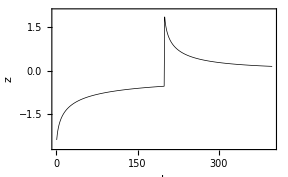

Fig. Chapter.FigureCaption  Simulated double potential step chronoamperogram. (n F/R T)E_1=-10, (n F/R T)E_2=10, k_s=1  cm · s^-1, and D=10^-5 cm^2 · s^-1.

## Chapter.Section Staircase voltammetry

Chapter.Section.Subsection Introduction

Staircase voltammetry is probably the most commonly used electroanalytical method. Though not generally thought of as a periodic method staircase voltammetry can be analyzed using the methods described in §8.4. The staircase sweep is shown in Fig. Chapter.FigureCaption. Staircase voltammetry gives slightly different results to analogue linear sweep voltammetry. Caution should therefore be exercised when using theories for analogue cyclic and linear sweep voltammetry to interpret staircase voltammetric data. When the current is sampled at the end of the potential step the staircase sweep will produce an analogue like response only at the limit of very small potential steps. Larger steps can lead to voltammograms that may appear to be under some kinetic restraint if interpreted using analogue theory. Unfortunately in the literature sweep rates are generally reported rather than step sizes and step periods.

The staircase waveform is readily simulated with the aid of the Mod function. In the example below a staircase waveform is generated with a step height of 2*Pi/Ω.

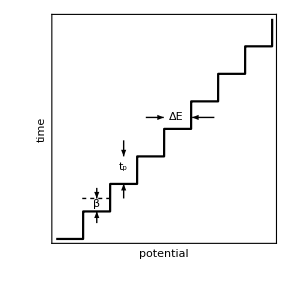

```mathematica
ClearAll[Ω,τ,staircase];

Ω=12.8*Pi ;
τ=20/2^16;

staircase=Table[((j*τ)-Mod[j*τ,2*Pi/Ω]),{j,1,2^12//N}];

ListPlot[staircase,
AspectRatio-> 1,
Axes->False,
Frame-> True,
FrameTicks-> None,
FrameLabel-> {"potential","time",None,None},
Joined-> True,
PlotStyle-> GrayLevel[0],
ImageSize-> {288,288},
RotateLabel-> False,
Epilog-> {
Text[DisplayForm[Row[{"Δ","",Style["E",FontFamily->"Times New Roman",FontSlant->"Italic"]}]],{2280,0.69}],
Arrowheads[{0,0.03}],
Arrow[{{1700,0.69},{2040,0.69}}],
Arrow[{{3000,0.69},{2580,0.69}}],
Text[DisplayForm[RowBox[{TraditionalForm[MakeBoxes[Subscript[t,p],TraditionalForm]]}]],{1280,0.41}],
Arrow[{{1280,0.56},{1280,0.469}}],
Arrow[{{1280,0.23},{1280,0.3125}}],
Text[DisplayForm[TraditionalForm[β]],{770,0.20}],
Arrow[{{770,0.29},{770,0.23}}],
Arrow[{{770,0.09},{770,0.156}}],
Dashing[{0.01,0.01}],
Line[{{495,0.23},{1010,0.23}}]}
]
SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  A staircase waveform with step height Δ E. The current is typically sampled at a fraction, β, of the step of period t_p.

The simulation of the staircase sweep was outlined in the previous chapter when a square wave on top of an underlying staircase sweep was simulated. The equation for the potential profile is:

```mathematica
ξ=Exp[α*(upperLimit-Δ𝔼s*((k-Mod[k,tN])/tN))];
```

where tN is the number if increments in each staircase step. The file sc5Rev.dat contains data from a simulated staircase voltammogram. note

```mathematica
ClearAll[c];

c=<<sc5Rev.dat;
```

The parameters used to obtain this data are given below:

```mathematica
ClearAll[a,𝔻,cycles,Δ𝔼s,upperLimit,𝕥,tN,τ,n];

a=1.05;(*grid expansion factor*)
𝔻=2.;(*model diffusion coefficient*)
cycles=102;(*number of steps*)
Δ𝔼s=𝒻*0.005;(*dimensionless staircase step size = f × amplitude in V*)
upperLimit=10.;(*initial potential versus the formal potential*)
𝕥=cycles*Δ𝔼s;(*dimensionless potential scan range*)
tN=100;(*number of increments per staircase step*)
τ=𝕥/n; (*calculation of the incremental potential step*)
n=10200;(*number of time steps in simulation*)
```

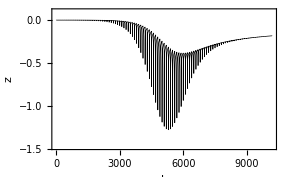

```mathematica
scv1=Map[(((2.+a)*a*#⟦1⟧-((1.+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*(n-1))/(2.*a^2*(1.+a)*𝕥)))&,c];

plot1=ListPlot[scv1,optionA,PlotRange-> {{0,n},{Min[scv1]-.2,Max[scv1]+.1}}]
```

Fig. Chapter.FigureCaption  Simulated reversible staircase voltammogram. Simulation parameters: ΔE=5  mV, Ω=16.13, t_p=0.1  s, k_s=10^3 cm · s^-1, n=10  200.

### Chapter.Section.Subsection Analysis of sampling point

If the current is sampled at the end of the step, i.e. β=1, then staircase and linear sweep voltammetry are only equivalent at the limit ΔE → 0. In practice the two have been shown to be indistinguishable for ΔE < 0.26  mV. It is possible however to produce a staircase voltammogram with identical peak potentials to a linear sweep voltammogram with step sizes of up to nΔE = 8  mV by sampling the current at a point other than the end of the potential step. Although theoretical predictions have indicated that by sampling the current at a fraction β, of 0.25 for reversible reactions, numerical simulation suggests that a value of between about 0.33 and 0.35 gives results in better agreement with linear sweep voltammetry. In instances when β values of both 0.25 and between 0.33 and 0.35 have been tested the later seems to give peak heights and positions closest to those expected for a linear sweep. An example is given in Fig. Chapter.FigureCaption.

```mathematica
ClearAll[cv];

cv=<<cvRev2.dat;
```

If this file is not already in your path and you do not wish to add that directory to your path you can browse for the file using this command:

ClearAll[cv];

cv=Get[SystemDialogInput["FileOpen"]];

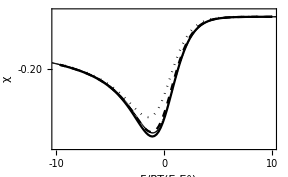

```mathematica
(*current sampled at the end of the step*)
staircaseData=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,tN-1,Length[scv1],tN}];

(*current sampled at 0.33 of the step*)
staircaseData2=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,33,Length[scv1],tN}];

(*current sampled at 0.25 of the step*)
staircaseData3=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,25,Length[scv1],tN}];

plot2a=ListPlot[staircaseData,PlotStyle->Directive[Black,Dotted]];
plot2b=ListPlot[staircaseData2,PlotStyle-> Directive[Black,Dashed]];
plot2c=ListPlot[staircaseData3,PlotStyle->Black];

Show[plot2a,plot2b,plot2c,optionDC,Epilog-> {AbsolutePointSize[1],Black,Point/@cv}]
```

Fig. Chapter.FigureCaption  Simulated reversible staircase voltammogram with the dimensionless current sampled at (bottom to top) α=1.0, 0.33, and 0.25, and simulated reversible linear sweep (•••••). Same staircase simulation parameters as in Fig Chapter.4. Linear sweep simulation parameters n=3200.

Importantly a particular chosen value of sampling point does not provide universal equivalence between staircase and linear sweep over the entire voltammogram. For irreversible reactions, or more generally for reactions described by Volterra equations of the second kind (§5.7), theoretical predictions have indicated that by sampling the current at β=0.5 peak potentials should agree with those obtained from linear sweeps. An irreversible staircase voltammogram is shown in Fig. Chapter.FigureCaption and the sampled current staircase voltammogram is shown in Fig. Chapter.FigureCaption.

```mathematica
ClearAll[c];
c=<<sc5Irrev.dat;
```

```mathematica
ClearAll[a,𝔻,cycles,Δ𝔼s,upperLimit,tN,τ,n];
a=1.05;(*grid expansion factor*)
𝔻=2.;(*model diffusion coefficient*)
cycles=180;(*number of steps*)
Δ𝔼s=𝒻*0.005;(*dimensionless staircase step size = f × amplitude in V*)
upperLimit=0.;(*initial potential versus the formal potential*)
𝕥=cycles*Δ𝔼s;(*dimensionless potential scan range*)
tN=100;(*number of increments per half square wave cycle*)
τ=𝕥/n; (*calculation of the incremental potential step*)
n=18000;(*number of time steps in simulation*)
```

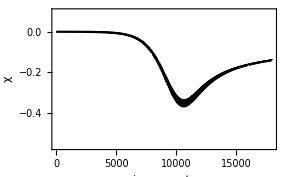

```mathematica
scv1=Map[(((2.+a)*a*#⟦1⟧-((1.+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*(n-1))/(2.*a^2*(1.+a)*𝕥)))&,c];
plot1=ListPlot[scv1,optionA1,PlotRange-> {{0,n},{Min[scv1]-.2,Max[scv1]+.1}}]
```

Fig. Chapter.FigureCaption  Simulated irreversible staircase voltammogram. Simulation parameters: ΔE=5  mV, Ω=16.13, t_p=0.1  s, k_s=10^-6 cm · s^-1, n=18  000.

The sampled current staircase voltammogram can be compared to an irreversible linear sweep voltammogram.

```mathematica
ClearAll[cv2];

cv2=<<cvIrrev.dat;
```

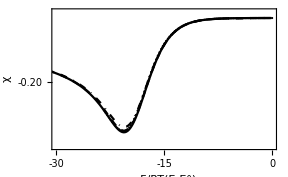

```mathematica
(*current sampled at the end of the step*)
staircaseData=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,tN-1,Length[scv1],tN}];
(*current sampled at 0.50 of the step*)
staircaseData2=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,tN+49,Length[scv1],tN}];

(*current sampled at 0.33 of the step*)
staircaseData3=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,tN+32,Length[scv1],tN}];
plot2a=ListPlot[staircaseData,PlotStyle->Directive[Black,DotDashed]];
plot2b=ListPlot[staircaseData2,PlotStyle-> Directive[Black,Dashed]];
plot2c=ListPlot[staircaseData3,PlotStyle->Black];

Show[plot2a,plot2b,plot2c,optionDC2,Epilog-> {AbsolutePointSize[1.5],Black,Point/@ cv2⟦1;;-1;;6⟧}]
```

Fig. Chapter.FigureCaption  Simulated irreversible staircase voltammogram with the dimensionless current sampled at (lines from bottom to top) β=1.0, 0.5, and 0.33 and simulated reversible linear sweep (•••••).

Excellent agreement between the irreversible linear sweep voltammogram and the irreversible staircase voltammogram, over the entire voltammogram, is obtained with β=0.5. With β=0.33 a good fit is also obtained although a flatter peak is observed.

### Chapter.Section.Subsection Analysis of the dc component

Since the size of the staircase steps is relatively small separation of the ac components from the dc components is not that easy. The dc component can however be removed from the data by using a moving average of width equal to the number of time steps per staircase step. The result of the moving average is shown in Fig. Chapter.FigureCaption. This data can then be subtracted from the raw data to produce a ‘dc free’ voltammogram.

The moving average filter averages over N points with N being the number of increments per cycle.

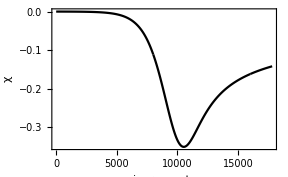

```mathematica
ClearAll[data2];
data2=MovingAverage[scv1,tN];
data2=MovingAverage[data2,tN];

plot3=ListPlot[data2,optionA1]
```

Fig. Chapter.FigureCaption  Staircase voltammogram from Fig. Chapter.FigureCaption after application of a moving average filter.

The moving average chops the data list. To subtract the unfiltered data, scv1, from the filtered data, data2, we need to align the lists. We do this by first determining the length of the overhang.

```mathematica
ClearAll[oh];
oh=Length[scv1]-Length[data2]
```

198

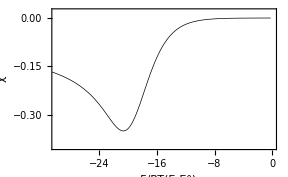

```mathematica
convert2[upperLimit_,oh_,τ_][i_,{j_}]:={upperLimit-(oh*τ/2.)-(τ*j),i}
scv3=MapIndexed[convert2[upperLimit,oh,τ],data2];

plot2=ListPlot[scv3,optionDC2]
```

Fig. Chapter.FigureCaption  Staircase voltammogram from Fig. Chapter.FigureCaption after application of a moving average filter.

The peak height and peak position are now obtained. Better accuracy is obtained by increasing the magnitude of n.

```mathematica
peakHeight=Min[scv3⟦All,2⟧];
Select[scv3,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at -20674./f mV with height -0.350539

After being isolated from the staircase voltammogram the dc voltammogram can be compared with the linear sweep voltammogram.

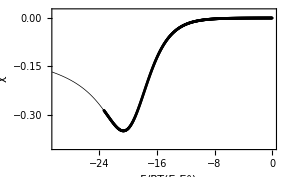

```mathematica
plot2=ListPlot[scv3,optionDC2,Epilog-> {AbsolutePointSize[2],Black,Point/@cv2}]
```

Fig. Chapter.FigureCaption  Comparison between the dc component removed from the staircase voltammogram in Fig. Chapter.FigureCaption and an irreversible linear sweep voltammogram simulated by numerical integration.

### Chapter.Section.Subsection Analysis in the frequency domain

To analyze a staircase sweep using the Fourier transform method outlined in Chapter 7 it is helpful to think of a staircase sweep as being a backward sawtooth wave superimposed on a linear sweep. The equation for a staircase sweep of step amplitude Δ E and step time width t_p is given by the Fourier series approximation:

E(t)=E+(Δ E)/t_p t-(Δ E)/π∑_(n=1)^∞ 1/n sin ((2nπt)/t_p)

```mathematica
ClearAll[staircase];

staircase[max_,tp_,t_]:=t/tp+1/Pi*∑_(k=1)^max (1/k*Sin[(2*Pi*k*t)/tp])
```

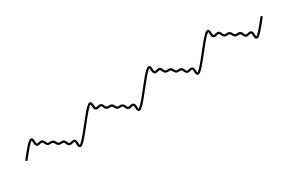

```mathematica
Plot[staircase[5,2*Pi,x],{x,-4*π,4*π},Axes-> False,Frame-> False]
```

Fig. Chapter.FigureCaption  Simulated staircase waveform.

As the number of terms, n, being summed in eqn (Chapter.EquationNumbered) increases the resulting plot becomes more ‘staircase’ like.

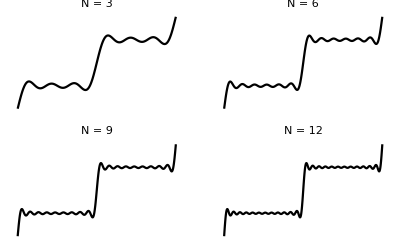

```mathematica
staircasePlot=GraphicsGrid[Table[Plot[Evaluate[staircase[3*(2*i+j),2*Pi,x]],{x,-2*π,2*π},
PlotStyle-> {RGBColor[0,0,0]},
Frame-> False,
Axes-> False,
PlotLabel->ToString[DisplayForm[TraditionalForm[N]]]<>" = "<>ToString[3*(2*i+j)],
BaseStyle-> {FontFamily-> "Times",Black}],{i,0,1},{j,1,2}],
ImageSize->400]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Staircase waveforms simulated using eqn (Chapter.EquationNumbered) with increasing value of n.

According to eqn (Chapter.EquationNumbered) when the Fourier transform of the staircase data is taken we expect to see multiples of the fundamental frequency.

```mathematica
powerSpectrumAxis[𝕥_][a_,{b_}]:={(b-1)/𝕥,a}
```

```mathematica
fourierData=Abs[Fourier[scv1]];
fourierData=MapIndexed[powerSpectrumAxis[𝕥],fourierData];
```

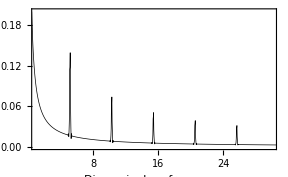

```mathematica
mainPlot=ListPlot[fourierData,optionMain,PlotRange-> {{1,30},{0,.2}}]
```

Fig. Chapter.FigureCaption  Power spectrum of simulated staircase voltammogram shown in Fig. Chapter.FigureCaption.

The dc component can be subtracted from this data to produce a ‘cleaner’ spectrum. The length of the dc data is shorter than the staircase data due to the use of the moving average filter to obtain the dc data. To subtract the dc data the staircase data list needs to be trimmed to the same length.

```mathematica
scv1Short=Drop[Drop[scv1,99],-99];

dcRemoved=MapThread[#1-#2&,{scv1Short,data2}];
```

```mathematica
fourierData=Abs[Fourier[dcRemoved]];
fourierData=MapIndexed[powerSpectrumAxis[𝕥],fourierData];
```

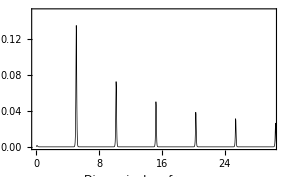

```mathematica
mainPlot2=ListPlot[fourierData,optionMain,PlotRange-> {{0,30},{0,0.15}}]
```

Fig. Chapter.FigureCaption  Power spectrum of simulated staircase voltammogram shown in Fig. Chapter.FigureCaption. after the removal of the dc component.

The components can be isolated from the power spectrum using the same approach as shown in Chapter 7.

```mathematica
ClearAll[fourierFilter];

fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];b=Join[Table[0.,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0.,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0.,{j,1,x-1}]];Re[InverseFourier[b]]];
```

```mathematica
newdata=fourierFilter[dcRemoved,Round[n/tN]-10,Round[n/tN]+10];

(*add dimensionless potential scale to the x axis*)
firstComponent=MapThread[{#1⟦1⟧,#2}&,{scv3,newdata}];
```

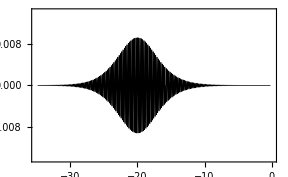

```mathematica
ListPlot[firstComponent,
ImagePadding->{{Inherited,5},{Inherited,5}},
PlotRange->{{upperLimit-𝕥,upperLimit},{Min[newdata]-0.005,Max[newdata]+0.005}}]
```

Fig. Chapter.FigureCaption  First component of the staircase waveform isolated from the power spectrum shown in Fig. Chapter.FigureCaption.

## Chapter.Section Normal pulse voltammetry

Chapter.Section.Subsection Introduction

In normal pulse voltammetry, after a period τ' at a resting potential, a pulse is applied and the current is measured at time τ (Fig Chapter.FigureCaption). The potential then returns to the resting potential. After another period τ' another pulse is applied this time with an increased magnitude. The magnitude of the potential pulse increases each time the pulse is applied.

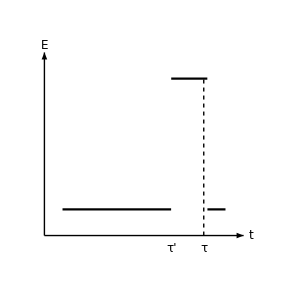

```mathematica
ClearAll[u,k];

u[k_]=UnitStep[(k-85)(k-95)(k-200)];

Plot[.2+u[Mod[k,95]],{k,55,100},
Frame-> False,
AspectRatio-> 1,
Axes->False,
AxesOrigin-> {45,0},
PlotRange-> {{45,110},{-.2,1.6}},
Ticks-> None,
Epilog-> {
Text[Style["E",FontFamily-> "Times",Italic,12],{50,1.45}],Text[Style["t",FontFamily-> "Times",Italic,12],{107,0}],
Text[Style["τ'",12],{85,-.1}],
Text[Style["τ",12],{94,-.1}],
Arrow[{{50,0},{105,0}}],
Arrow[{{50,0},{50,1.4}}],
Dashing[{0.01,0.01}],
Line[{{94,0},{94,1.2}}]}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Diagram showing how a the pulse is sampled in normal pulse voltammetry.

The equation for the current in normal pulse voltammetry is

i(t)=(nFA c^*D^(1/2))/((π^(1/2)(τ-τ'))^(1/2))

The current is defined as

i(t)=-n F A (D((∂c_O(x,t))/(∂x)))_(x=0)

In discrete form this becomes

i(k) =nFA c^*D/(2Δx)(-3 c_O_1^k+4 c_O_2^k-c_O_3^k)

Equating eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

(i(k))/(n F A c^*)=D^(1/2)/((π^(1/2)(τ-τ'))^(1/2))=D/(2Δx)(-3 c_O_1^k+4 c_O_2^k-c_O_3^k)

Substituting Δ x=(D Δ t/D)^(1/2) and Δ t=(τ-τ')/(p-1), where p is the number of increments used to simulate the pulse, into eqn (Chapter.EquationNumbered) gives

(i(k))/(nFA c^*)=D^(1/2)/((π^(1/2)(τ-τ'))^(1/2))
=((D^(1/2)(D(p-1)))^(1/2))/(2(τ-τ')^(1/2))(-3 c_O_1^k+4 c_O_2^k-c_O_3^k)

Rearranging eqn (Chapter.EquationNumbered) gives the equation for the dimensionless current in normal pulse voltammetry.

i(k)=(i(k)π^(1/2))/(nFA c^*)((τ-τ')/D)^(1/2)
=((π^(1/2)(D(p-1)))^(1/2))/2(-3 c_O_1^k+4 c_O_2^k-c_O_3^k)

The dimensionless rate constant can be determined from the Butler-Volmer equation.

i(t)=nFA c^*k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

Multiplying both sides by π^(1/2)/(nFA c^*)((τ-τ')/D)^(1/2) gives

(i(k)π^(1/2))/(nFA c^*)((τ-τ')/D)^(1/2)=k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with the dimensionless rate constant defined as

k_s=π^(1/2)(k_s((τ-τ')/D))^(1/2)

From eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) we have

((π^(1/2)(D(p-1)))^(1/2))/2(-3 c_O_1^k+4 c_O_2^k-c_O_3^k)=k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

Therefore

-3 c_O_1^k+4 c_O_2^k-c_O_3^k=k_s^*(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with

k_s^*=(2 k_s)/((π^(1/2)(D(p-1)))^(1/2))

With these definitions the normal pulse voltammogram can be simulated after a method to construct the pulse has been developed.

### Chapter.Section.Subsection Constructing the pulse

A pulse can be generated using the UnitStep function. For example:

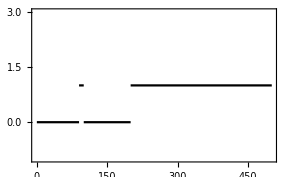

```mathematica
ClearAll[u,k];

u[k_]=UnitStep[(k-90)*(k-100)*(k-200)];
Plot[u[k],{k,0,501},PlotRange-> {-1,3},PlotPoints-> 500,AxesOrigin-> {-1,-1}]
```

We want the pulse to repeat at fixed intervals. This can be done by getting the argument of the unit step function to return to ‘rest’ at fixed intervals. This requires the use of Mod. For example:

```mathematica
Table[Mod[k,100],{k,0,200}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,0}

By making the argument of the unit step function some function of Mod a repeating pulse can be constructed.

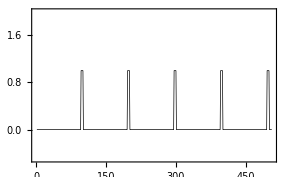

```mathematica
u[k_]=UnitStep[(k-95)(k-100)(k-200)];

ListPlot[Table[u[Mod[k,100]],{k,0,505}],InterpolationOrder->1,PlotRange-> {-.5,2},AxesOrigin-> {-.1,-0.5}]
```

To ensure that no errors are occurring a pulse list can be generated and checked to ensure that the pulse length is identical throughout.

```mathematica
test=Table[Ceiling[k/100]*u[Mod[k,100]],{k,0,999}];
Length/@Split[test]
```

{95,5,95,5,95,5,95,5,95,5,95,5,95,5,95,5,95,5,95,5}

Finally we need to increase the pulse magnitude each time it is applied.

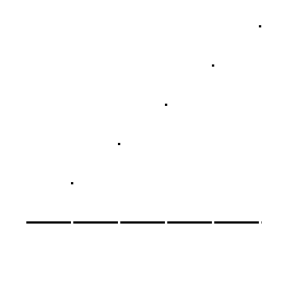

```mathematica
Plot[Ceiling[k/100]*u[Mod[k,100]],{k,0,501},PlotRange-> {-1,5},PlotPoints-> 500,Axes-> False,Frame-> False,AspectRatio-> 1]
```

Fig. Chapter.FigureCaption  An example of the generation of the pulse sequence in normal pulse voltammetry. The potential returns to the start potential after successive pulse. The magnitude of the pulse increase by an amount Δ E with each pulse.

The potential dependent function used in the simulation of normal pulse voltammograms will therefore be:

ξ=Exp[upperLimit-Δ𝔼p*Ceiling[k/tL]*u[Mod[k,tL]]];

The full implementation is given in the notebook ImplicitNP-RMExp.nb.

Some simulated data is contained in the file np5.dat.

```mathematica
ClearAll[c];
c=<<np5.dat;
```

If this file is not already in your path and you do not wish to add that directory to your path you can browse for the file using this command:

```mathematica
ClearAll[Δ𝔼p,upperLimit,𝔻,p,tL,a,m];
Δ𝔼p=𝒻*0.005;(*dimensionless normal pulse step size = f × amplitude in V*)
upperLimit=8.;(*initial potential versus the formal potential*)
𝔻=2.;(*model diffusion coefficient*)
p=5;(*length of the pulse*)
tL=100;(*length of pulse plus length of rest time*)
a=1.05;(*grid expansion factor*)
m=77;(*number of spacial grid points*)
```

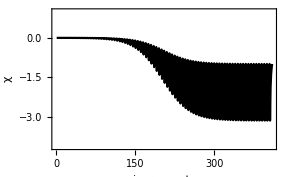

```mathematica
npv2=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];

plot1=ListPlot[npv2,optionA2,PlotRange-> {{0,Length[c]},{Min[npv2]-1,Max[npv2]+1}}]
```

Fig. Chapter.FigureCaption  A simulated reversible normal pulse voltammogram. Simulation parameters: p=5, Δ E=5  mV, D=2.

The normal pulse voltammogram can be re-plotted after taking the values of the dimensionless current immediately prior to the end of a pulse.

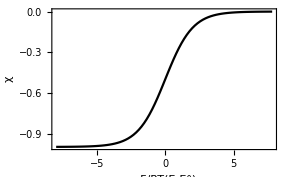

```mathematica
normalPolarography=Table[{upperLimit-(Δ𝔼p*k/p),npv2⟦k⟧},{k,p,Length[npv2],p}];

normalPlot2=ListPlot[normalPolarography,optionB]
```

Fig. Chapter.FigureCaption  A simulated reversible normal pulse voltammogram with current sampling at the end of each pulse.

## Chapter.Section Differential pulse voltammetry

Chapter.Section.Subsection Introduction

In differential pulse voltammetry the pulse sequence is superimposed on a staircase ramp of step height Δ E_s. After a period τ' at a given step potential a pulse of magnitude Δ E_p is applied. the current is measured at τ' immediately prior to the application of the pulse and again at time τ during the application of the pulse (Fig Chapter.FigureCaption). The potential then returns to the potential of the next step in the staircase and this sequence is repeated. After another period τ' another pulse is applied this time with an increased magnitude. The output is the differential current, δ i, which is the difference between the current sampled at τ' and the current sampled at τ.

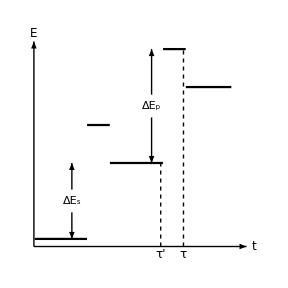

```mathematica
ClearAll[stepLength,ts,stepHeight,th,pulseHeight,tp,pulseWidth,tw,u,label1,label2];

stepLength=100;
ts=stepLength;
stepHeight=1/ts;
th=stepHeight;
pulseHeight=1.5;
tp=pulseHeight;
pulseWidth=30;
tw=ts-pulseWidth;

u[k_]=UnitStep[(k-tw)(k-ts)(k-200)];

label1=DisplayForm[Row[{"Δ","",Subscript[Style["E",FontFamily->"Times",Italic,12],Style["p",FontFamily-> "Times",8]]}]];

label2=DisplayForm[Row[{"Δ","",Subscript[Style["E",FontFamily-> "Times",Italic,12],Style["s",FontFamily-> "Times",8]]}]];

Plot[.1+th*(k-Mod[k,ts])+tp*u[Mod[k,ts]],{k,1,260},
AspectRatio-> 1,
Axes->False,
Frame-> False,
PlotRange-> {{-10,300},{-.2,2.9}},
Epilog-> {
Text[Style["E",FontFamily-> "Times",Italic,12],{0,2.8}],Text[Style["t",FontFamily-> "Times",Italic,12],{290,0}],
Text[Style["τ'",12],{167,-.1}],
Text[Style["τ",12],{197,-.1}],
Text[label1,{155,1.85}],
Arrow[{{155,2.0},{155,2.6}}],
Arrow[{{155,1.7},{155,1.1}}],
Text[label2,{50,0.6}],
Arrow[{{50,.75},{50,1.1}}],
Arrow[{{50,.45},{50,0.1}}],
Arrow[{{0,0},{280,0}}],
Arrow[{{0,0},{0,2.7}}],
Dashing[{0.01,0.01}],
Line[{{167,0},{167,1.1}}],
Line[{{197,0},{197,2.6}}]}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Diagram showing how a the pulse is sampled in differential pulse voltammetry.

The equation for the differential pulse voltammetric current for a reversible reaction is

δ i(t)=i(τ)-i(τ')
=(nFA c^*D^(1/2))/((π^(1/2)(τ-τ'))^(1/2))((P(1-ϑ^2))/((ϑ+P)(1+P ϑ)))

with

P=γexp((n F)/(R T)(E+(Δ E_p)/2-E°))

ϑ=exp((n F)/(R T)(Δ E_p)/2)

and γ=(D_O/D_R)^(1/2). The current given in terms of the discrete form of the flux is given by eqn (Chapter.EquationNumbered). Equating eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

(δ i(k))/(nFA c^*)=D^(1/2)/((π^(1/2)(τ-τ'))^(1/2))((P(1-ϑ^2))/((ϑ+P)(1+P ϑ)))
=D/(2Δx)(-3 c_1^k+4 c_2^k-c_3^k)

Making the substitutions described in the previous section, Δ x=(D Δ t/D)^(1/2) and Δ t=(τ-τ')/(p-1), and rearranging gives the equation for the dimensionless current in differential pulse voltammetry.

δi(k)=(δ i(k)π^(1/2))/(nFA c^*)((τ-τ')/D)^(1/2)
=((π^(1/2)(D(p-1)))^(1/2))/2(-3 c_1^k+4 c_2^k-c_3^k)
=((P(1-ϑ^2))/((ϑ+P)(1+P ϑ)))

The dimensionless current function is a gaussian shaped peak with a height dependent on the magnitude of the pulse.

```mathematica
ClearAll[P,𝔼,ϑ]

Solve[D[(P[𝔼]*(1-ϑ[𝔼]^2))/((ϑ[𝔼]+P[𝔼])*(1+P[𝔼] *ϑ[𝔼])),P[𝔼]]== 0,P[𝔼]]//Simplify
```

{{P[𝔼]→-1},{P[𝔼]→1}}

The peak height occurs when P=1 therefore the peak dimensionless current is

```mathematica
(P*(1-ϑ^2))/((ϑ+P)*(1+P *ϑ))/.P-> 1//Simplify
```

(1-ϑ)/(1+ϑ)

The peak differential current is therefore given by

δ (i(k))_p=(1-ϑ)/(1+ ϑ)

The peak heights for typical pulse sizes is calculated below:

```mathematica
ClearAll[f]

f=38.9217;

(1-Exp[f*#/2.])/(1+Exp[f*#/2.])&/@{.005,.010,.025,.050,.100}
```

{-0.0486138,-0.0969983,-0.238573,-0.451451,-0.750038}

### Chapter.Section.Subsection Constructing the pulse

The differential pulse sequence can be simulated by combining the potential sequences of staircase voltammetry and normal pulse voltammetry. For example the staircase potential is generated using Mod:

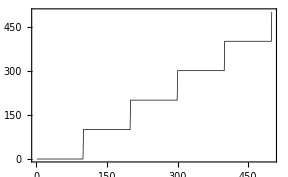

```mathematica
staircase=Table[k-Mod[k,100],{k,1,500}];
ListPlot[staircase]
```

The normal pulse is generated by combining the UnitStep and Mod functions.

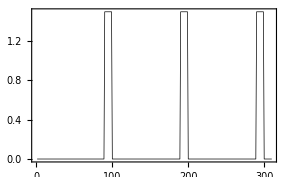

```mathematica
ClearAll[u,k,pulse]

u[k_]=UnitStep[(k-90)(k-100)(k-200)];

pulse=Table[1.5*u[Mod[k,100]],{k,1,310}];
ListPlot[pulse]
```

Combining these two sequences yields the differential pulse sequence.

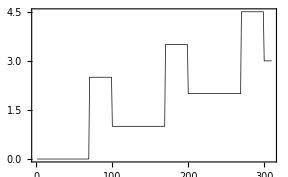

```mathematica
ClearAll[stepLength,ts,stepHeight,ΔEs,pulseHeight,ΔEp,pulseWidth,tw,u,diffPulse,k]

stepLength=100;
ts=stepLength;
stepHeight=1/ts;
ΔEs=stepHeight;
pulseHeight=2.5;
ΔEp=pulseHeight;
pulseWidth=30;
tw=ts-pulseWidth;

u[k_]=UnitStep[(k-tw)(k-ts)(k-200)];

diffPulse=Table[ΔEs*(k-Mod[k,ts])+ΔEp*u[Mod[k,100]],{k,1,310}];

ListPlot[diffPulse]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  An example of the generation of the pulse sequence in normal pulse voltammetry. The potential returns to the start potential after successive pulse. The magnitude of the pulse increase by an amount Δ E with each pulse.

```mathematica
test=Table[th*(k-Mod[k,ts])+tp*u[Mod[k,ts]],{k,0,999}];
Length/@Split[test]
```

{70,30,70,30,70,30,70,30,70,30,70,30,70,30,70,30,70,30,70,30}

The potential dependent function used in the simulation of differential pulse voltammograms will therefore be:

ξ=Exp[upperLimit-(ΔEs/ts)*(k-Mod[k,ts])-ΔEp*u[Mod[k,ts]]];

The full implementation is given in the notebook ImplicitDP-RMExp.nb.

Some simulated data is contained in the file dp50.dat.

```mathematica
ClearAll[c];
c=<<dp50.dat;
```

```mathematica
ClearAll[ΔEp,ΔEs,upperLimit,𝔻,p,ts,a,m];
ΔEp=𝒻*0.05;(*dimensionless pulse size*)
ΔEs=𝒻*0.005;(*dimensionless staircase step size*)
upperLimit=10.;(*initial potential versus the formal potential*)
𝔻=2.;(*model diffusion coefficient*)
p=5;(*length of the pulse*)
ts=100;(*length of pulse plus length of rest time*)
a=1.05;(*grid expansion factor*)
m=79;(*number of spacial grid points*)
n=10300;
```

The raw concentration data is first converted to a dimensionless current.

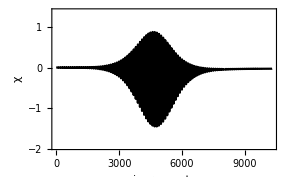

```mathematica
dpv1=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];
plot1=ListPlot[dpv1,optionA,PlotRange-> {{0,n},{Min[dpv1]-.5,Max[dpv1]+.5}}]
```

Fig. Chapter.FigureCaption  A simulated reversible differential pulse voltammogram. Simulation parameters: p=5, Δ E_p=50  mV, Δ E_s=5  mV, D=2.

The differential pulse voltammogram extracted from the raw data by taking the dimensionless current immediately before and after the pulse.

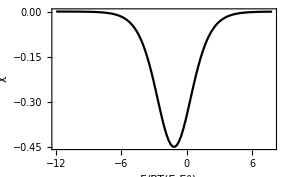

```mathematica
start=Table[dpv1⟦k⟧,{k,tw,Length[dpv1],ts}];

end=Table[dpv1⟦k⟧,{k,ts,Length[dpv1],ts}];

difference=Table[{upperLimit-ΔEp-(k*ΔEs),end⟦k⟧-start⟦k⟧},{k,1,Length[end]}];

diffPlot=ListPlot[difference,optionB,PlotStyle-> {Red}]
```

Fig. Chapter.FigureCaption  A simulated reversible differential pulse voltammogram.

## Chapter.Section Summary

This chapter has demonstrated that any type of voltammetry can be simulated starting with a ‘base’ method and substituting the required waveform into the simulation method.

## Further Reading

Miaw, L. L.-H., Boudreau, P. A., Pichler, M. A., and Perone, S. P. (1978). Analytical Chemistry, 50, 1988-96.
Seralathan, M., Osteryoung, R. A., and Osteryoung, J. G. (1986). Journal of Electroanalytical Chemistry, 214, 141-56.
Seralathan, M., Osteryoung, R. A., and Osteryoung, J. G. (1987). Journal of Electroanalytical Chemistry, 222, 69-100.
Stefani, S. and Seeber, R. (1982). Analytical Chemistry, 54, 2524-2530.